```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"fourdiff.wl"
```

```mathematica
Nt=128;
```

```mathematica
X=Get["dim3.5000HR_fromCE.res"][[1]]//N;
```

```mathematica
fcmodes=X[[1]]+I*X[[2]];
Psicmodes=X[[3]]+I*X[[4]];
upmodes=X[[5]]+I*X[[6]];
```

```mathematica
fcFourier=Riffle[Join[fcmodes,Reverse[Conjugate[fcmodes[[2;;-2]]]]],0,{2,-1,2}];
PsicFourier=Riffle[Join[Psicmodes,Reverse[Conjugate[Psicmodes]]],0,{1,-2,2}];
upFourier=Riffle[Join[upmodes,Reverse[Conjugate[upmodes]]],0,{1,-2,2}];
```

```mathematica
fcFourierdoub=double[fcFourier,Nt];
PsicFourierdoub=double[PsicFourier,Nt];
upFourierdoub=double[upFourier,Nt];
```

```mathematica
{fclistdoub,psiclistdoub,uplistdoub}=Re@(Sqrt[2Nt]InverseFourier/@{fcFourierdoub,PsicFourierdoub,upFourierdoub});
```

```mathematica
Export["fc.dat",fclistdoub]
```

fc.dat

```mathematica
Export["psic.dat",psiclistdoub]
```

psic.dat

```mathematica
Export["Up.dat",uplistdoub]
```

Up.dat

```mathematica
Export["Delta.dat",X[[-1,1]]]
```

Delta.dat

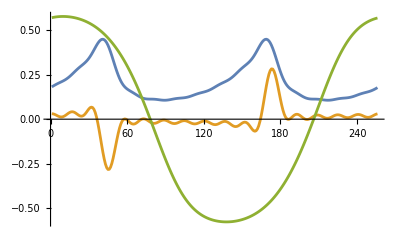

```mathematica
ListPlot[Re/@{fclistdoub,1/500 psiclistdoub,uplistdoub},Joined->True]
```

### Extend to 256 modes

```mathematica
Ntini=Length[X[[3]]]*4
```

128

```mathematica
Nt=256;
```

```mathematica
X={
 Join[X[[1]],ConstantArray[0,(Nt-Ntini)/4]],
 Join[X[[2]],ConstantArray[0,(Nt-Ntini)/4]],
 Join[X[[3]],ConstantArray[0,(Nt-Ntini)/4]],
 Join[X[[4]],ConstantArray[0,(Nt-Ntini)/4]],
 Join[X[[5]],ConstantArray[0,(Nt-Ntini)/4]],
 Join[X[[6]],ConstantArray[0,(Nt-Ntini)/4]],
 X[[7]]
 };
```

```mathematica
fcmodes=X[[1]]+I*X[[2]];
Psicmodes=X[[3]]+I*X[[4]];
upmodes=X[[5]]+I*X[[6]];
```

```mathematica
fcFourier=Riffle[Join[fcmodes,Reverse[Conjugate[fcmodes[[2;;-2]]]]],0,{2,-1,2}];
PsicFourier=Riffle[Join[Psicmodes,Reverse[Conjugate[Psicmodes]]],0,{1,-2,2}];
upFourier=Riffle[Join[upmodes,Reverse[Conjugate[upmodes]]],0,{1,-2,2}];
```

```mathematica
fcFourierdoub=double[fcFourier,Nt];
PsicFourierdoub=double[PsicFourier,Nt];
upFourierdoub=double[upFourier,Nt];
```

```mathematica
{fclistdoub,psiclistdoub,uplistdoub}=Re@(Sqrt[2Nt]InverseFourier/@{fcFourierdoub,PsicFourierdoub,upFourierdoub});
```

```mathematica
Export["fc.dat",fclistdoub]
```

fc.dat

```mathematica
Export["psic.dat",psiclistdoub]
```

psic.dat

```mathematica
Export["Up.dat",uplistdoub]
```

Up.dat

```mathematica
Export["Delta.dat",X[[-1,1]]]
```

Delta.dat